```mathematica
Manipulate[PDF[NormalDistribution[{mu, sig}]], {mu, 0, 10}, {sig, 0, 10}]
```

```mathematica
Plot[PDF[NormalDistribution[{}], x], {x, -5, 5}]
```

```mathematica
Plot[PDF[NormalDistribution[0,σ],x],{x,-6,6}]
```

```mathematica
Manipulate[DiscretePlot[PDF[NormalDistribution[mu,sig],x],{x,-20,20}, PlotRange->All], {{mu, 0}, -5, 10}, {sig, .1, 10}]
```

```mathematica
Manipulate[DiscretePlot[PDF[BinomialDistribution[n,p],x],{x, 0, 500}, PlotRange->All], {n, 0, 1000, 1}, {p, 0, 1}]
```

```mathematica
Manipulate[Plot[CDF[BinomialDistribution[n,p],x],{x, 0, 40}, PlotRange->All], {{n,30}, 0, 1000, 1}, {{p, 0.5}, 0, 1}]
```

```mathematica
Solve[CDF[BinomialDistribution[30,0.5], x] >= 0.95, x]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[(Piecewise[{{BetaRegularized[0.5,30-Floor[x],1+Floor[x]], 0≤x<30}, {1, x≥30}, {0, True}}])≥0.95,x]

```mathematica
Minimize[{c,CDF[BinomialDistribution[30, 10/20], c] >= 95/100 && 
   0 < c <= 100}, c, Integers][[1]]
```

19

```mathematica
Manipulate[DiscretePlot[Minimize[{c, 
  CDF[BinomialDistribution[n, p/20], c] >= 95/100 && 
   0 < c <= 100}, c, Integers][[1]]/n, {n, 1, 100, 1}, PlotRange->{0.1, 1}], {{p, 10}, 0, 20, 1}]
```

```mathematica
DiscretePlot[Minimize[{c, 
  CDF[BinomialDistribution[n/(2^(3-1)), 10/20], c] >= 95/100 && 
   0 < c <= 200}, c, Integers][[1]]/(n/(2^(3-1))), {n, 2^(5-1), 1000, 2^(5-1)}, PlotRange->{0.5, 1}, PlotStyle -> Red],
   DiscretePlot[Minimize[{c, 
  CDF[BinomialDistribution[n/(2^(5-1)), 10/20], c] >= 95/100 && 
   0 < c <= 200}, c, Integers][[1]]/(n/(2^(5-1))), {n, 2^(5-1), 1000, 2^(5-1)}, PlotRange->{0.5, 1}, PlotStyle -> Orange]
```

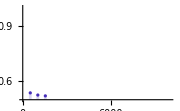
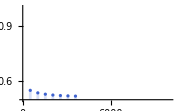
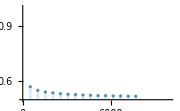
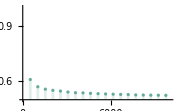
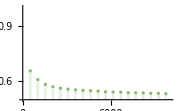
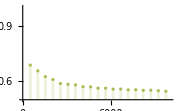
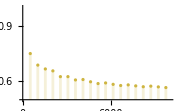
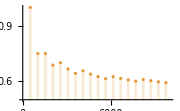

```mathematica
Row[Table[
DiscretePlot[Minimize[{c, 
  CDF[BinomialDistribution[n/(2^(s-1)), 10/20], c] >= 95/100 && 
   0 < c <= 1000}, c, Integers][[1]]/(n/(2^(s-1))), {n, 2^(10-1), 10000, 2^(10-1)}, PlotRange->{{0, 10000}, {0.5, 1}}, PlotStyle->ColorData["Rainbow"][s/10], ImageSize->Small], {s, 1, 10}]]
```

```mathematica
Table[Minimize[{c, 
  CDF[BinomialDistribution[128/2^(s - 1), 10/20], c] >= 95/100 && 
   0 < c <= 200}, c, Integers][[1]]/128/(2^(s-1)) // Evaluate, {s, 1, 5}]
```

{11/1024,11/1024,11/1024,11/1024,11/1024}

```mathematica
Table[CDF[BinomialDistribution[20/2, 10/20], 20] // Evaluate, {s, 1, 5}]
```

{1,1,1,1,1}

```mathematica
s = 1;
Show[
(*	DiscretePlot[Minimize[{c, 
	CDF[BinomialDistribution[n/2^(1 - 1), 10/20], c] >= 95/100 && 
	0 < c <= 200}, c, Integers][[1]]/n/(2^(1-1)), {n, 2, 200, 2}, PlotRange->{0.5, 1}]*)
	DiscretePlot[Minimize[{c, 
	CDF[BinomialDistribution[n/2^(1), 10/20], c] >= 95/100 && 
	0 < c <= 200}, c, Integers][[1]]/n/(2^(1)), {n, 2, 200, 2}, PlotRange->{0.5, 1}]
]
```

```mathematica
ColorData["Rainbow"][0.5]
```

RGBColor[0.513417, 0.72992, 0.440682]

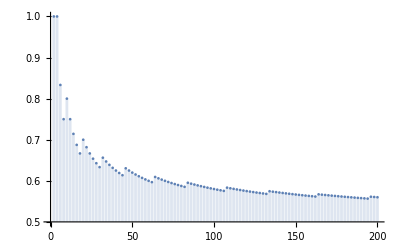

```mathematica
DiscretePlot[Minimize[{c, 
	CDF[BinomialDistribution[n/2^(0), 10/20], c] >= 95/100 && 
	0 < c <= 200}, c, Integers][[1]]/n/(2^(0)), {n, 2, 200, 2}, PlotRange->{0.5, 1}]
```

```mathematica
Minimize[{c, 
	CDF[BinomialDistribution[30/2^(1), 10/20], c] >= 95/100 && 
	0 < c <= 200}, c, Integers][[1]]/30
```

11/30

```mathematica
DiscretePlot[
 Table[PDF[BinomialDistribution[40, p], k], {p, {0.1, 0.5, 0.7}}] // 
  Evaluate, {k, 36}, PlotRange -> All, PlotMarkers -> Automatic]
```

```mathematica
y = x
```

```mathematica
Solve[BetaRegularized[0.5, 30 - Floor[x], 1 + Floor[x]] == 0.950631, x]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[BetaRegularized[0.5,30-Floor[x],1+Floor[x]]==0.950631,x]

```mathematica
ResourceFunction["DarkMode"][False]
```

```mathematica
Binomial[5, 5]
```

1

```mathematica
ResourceFunction["DarkMode"][True]
```

```mathematica
PercentForm[N[31/50]]
```

```mathematica
Plot[BinomialDistribution[10,.5],{x,-20,20}, PlotRange->All]
```

```mathematica
Plot[PDF[BinomialDistribution[n,p],k],
```

```mathematica
weights  = {0.6, 0.4}
```

```mathematica
Table[worb = RandomChoice[weights-> {1, 0}], 10]
```

```mathematica
ArrayPlot[{%}]
```

```mathematica
labels
```

```mathematica
getWeights[input_]:= If[input == 1, {0.7, 0.3}, {0.5, 0.5}]
```

```mathematica
getCES[n_]:=Module[{causes, effects, ces},
causes = Join[Table[0, n/2], Table[1, n/2]];
effects = RandomChoice[getWeights[#]-> {1, 0}]&/@ causes;
ces = MapThread[#1-> #2&, {causes, effects}];
Sort[Tally[ces]][[All, 2]];
Map[Count[ces, #]&,labelsNum]
]
```

```mathematica
getCES[100]
```

```mathematica
bars =Thread[Table[getCES[10], 20]];
lbars = MapThread[Labeled[#1, #2]&,{bars, labels}];
BarChart[lbars]
```

Let’s say I’m trying to prove if black causes black. How many cases do I need to prove this to a 95% certainty level. Assume a change in probability of 30%.
How much data / what kind of data do I need to suggest that black is causing black. Based on the data, there is no evidence of a dependence larger than p.

```mathematica
Labeled[#, ""]
```

```mathematica
Thread[%]
```

```mathematica
MapThread[#1->#2&,{{a, b}, {d, e, f, g}}]
```

```mathematica
BarChart[Labeled@@@Reverse[{{GrayLevel[1]->GrayLevel[0],24},{GrayLevel[1]->GrayLevel[1],26},{GrayLevel[0]->GrayLevel[0],47},{GrayLevel[0]->GrayLevel[1],3}},2]]
```

```mathematica
labels = {GrayLevel[0]->GrayLevel[0],GrayLevel[0]->GrayLevel[1],GrayLevel[1]->GrayLevel[0],GrayLevel[1]->GrayLevel[1]}
```

```mathematica
labelsNum = {1->1,1->0, 0->1, 0->0}
```

```mathematica
GrayLevel[1]
```

```mathematica
Permutations[{1, 0}]
```

```mathematica
Subsets[{1, 2, 3}]
```

```mathematica
Manipulate[ArrayPlot[Tuples[{0, 1}, n], Mesh-> True], {n, 1, 10, 1}]
```

```mathematica
Plot[2^x, {x, 1, 12}]
```

```mathematica
ArrayPlot[{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}]
```

```mathematica
RandomReal[1,{10,5}]
```

```mathematica
PieChart[RandomReal[1,{10,5}],ChartLayout->"Stacked"]
```